## Bare CZ gate sequence fidelities wrt initial states

Problem: Given an initial state ψ, and the gate sequence {CZ^(4k)}, find the fidelity of the final state under open system effects. Consider only T_(1,2) processes for the open system decoherence mechanisms.
Approach: We will solve the problem perturbatively. The CZ gate duration is assumed to be much smaller than the timescale associated with the decay of the system. Therefore, we will treat the gate and open system effects as separate channels. More concretely, if Φ represents the exact open system evolution under the CZ gate, we approximate Φ ≃ Ε ∘Υ where Υ is the unitary map corresponding to the 4 (now instantaneous) CZ gates and Ε is the pure decoherence map under T_(1,2) effects.

## Channel Υ - closed system gate

### Gate unitary

The CZ gate ideally has a π/4 amplitude, but it can have overrotation terms.

```mathematica
A_⊗B_:=KroneckerProduct[A,B];
Z=PauliMatrix[3];Id=IdentityMatrix[2];
H=π/4(Z⊗Z-Z⊗Id-Id⊗Z)+(η Z⊗Z+ϵ Z⊗Id+κ Id⊗Z);
(* Note that we removed the explicit time dependence, and we integrate over a unit time s.t. Integral[H] has an amplitude of π/4. The error amplitudes should be << π/4 *)
U=MatrixExp[-ⅈ H];
U/ⅇ^(ⅈ π/4)//MatrixForm//FullSimplify
U.U.U.U//MatrixForm//FullSimplify
```

(ⅇ^(-ⅈ (ϵ+η+κ)) | 0 | 0 | 0
0 | ⅇ^(-ⅈ (ϵ-η-κ)) | 0 | 0
0 | 0 | ⅇ^(ⅈ (ϵ+η-κ)) | 0
0 | 0 | 0 | -ⅇ^(ⅈ (ϵ-η+κ)))

(-ⅇ^(-4 ⅈ (ϵ+η+κ)) | 0 | 0 | 0
0 | ⅇ^(ⅈ (π+4 (-ϵ+η+κ))) | 0 | 0
0 | 0 | ⅇ^(ⅈ (π+4 (ϵ+η-κ))) | 0
0 | 0 | 0 | -ⅇ^(4 ⅈ (ϵ-η+κ)))

The unitary is of the form

```mathematica
({{ⅇ^(-ⅈ (ϵ+η+κ)), 0, 0, 0}, {0, ⅇ^(-ⅈ (ϵ-η-κ)), 0, 0}, {0, 0, ⅇ^(ⅈ (ϵ+η-κ)), 0}, {0, 0, 0, -ⅇ^(ⅈ (ϵ-η+κ))}})->({{ⅇ^(-ⅈ(α+β+γ)), 0, 0, 0}, {0, ⅇ^(ⅈ α), 0, 0}, {0, 0, ⅇ^(ⅈ β), 0}, {0, 0, 0, -ⅇ^(ⅈ γ)}})
```

where α = (-ϵ+η+κ), β = (ϵ+η-κ), γ =  (ϵ-η+κ).

### Gate channel

```mathematica
U=({{ⅇ^(-ⅈ(α+β+γ)), 0, 0, 0}, {0, ⅇ^(ⅈ α), 0, 0}, {0, 0, ⅇ^(ⅈ β), 0}, {0, 0, 0, -ⅇ^(ⅈ γ)}});
ConjugateTranspose[U].U//Simplify//MatrixForm
```

(ⅇ^(-ⅈ (α+β+γ-Conjugate[α+β+γ])) | 0 | 0 | 0
0 | ⅇ^(ⅈ (α-Conjugate[α])) | 0 | 0
0 | 0 | ⅇ^(ⅈ (β-Conjugate[β])) | 0
0 | 0 | 0 | ⅇ^(ⅈ (γ-Conjugate[γ])))

```mathematica
Υ[ρ_]:=U.ρ.ConjugateTranspose[U];
Refine[Υ[Table[Subscript[a, i,j],{i,1,4},{j,1,4}]],Assumptions->{α∈Reals,β∈Reals,γ∈Reals}]//MatrixForm
```

(a_(1,1) | ⅇ^(-ⅈ α-ⅈ (α+β+γ)) a_(1,2) | ⅇ^(-ⅈ β-ⅈ (α+β+γ)) a_(1,3) | -ⅇ^(-ⅈ γ-ⅈ (α+β+γ)) a_(1,4)
ⅇ^(ⅈ α+ⅈ (α+β+γ)) a_(2,1) | a_(2,2) | ⅇ^(ⅈ α-ⅈ β) a_(2,3) | -ⅇ^(ⅈ α-ⅈ γ) a_(2,4)
ⅇ^(ⅈ β+ⅈ (α+β+γ)) a_(3,1) | ⅇ^(-ⅈ α+ⅈ β) a_(3,2) | a_(3,3) | -ⅇ^(ⅈ β-ⅈ γ) a_(3,4)
-ⅇ^(ⅈ γ+ⅈ (α+β+γ)) a_(4,1) | -ⅇ^(-ⅈ α+ⅈ γ) a_(4,2) | -ⅇ^(-ⅈ β+ⅈ γ) a_(4,3) | a_(4,4))

## Channel Ε - pure decoherence

### Verify: Ε = Ε_1∘Ε_2

Ε_i is the pure decoherence channel acting only on qubit `i`. First compute the exact evolution given by the Lindblad master equation on the 2 qubits, with all the jump operators. Then compute the difference with the solution given by composing the 2 independent error channels Ε_1 and Ε_2.

#### Exact E

```mathematica
A_⊗B_:=KroneckerProduct[A,B];
```

```mathematica
Z=PauliMatrix[3];
SubMinus[σ]=(PauliMatrix[1]+ⅈ PauliMatrix[2])/2;
SubPlus[σ]=(PauliMatrix[1]-ⅈ PauliMatrix[2])/2;
Id=IdentityMatrix[2];
ℓ[ρ_,L_]:=L.ρ.ConjugateTranspose[L]-1/2(ConjugateTranspose[L].L.ρ+ρ.ConjugateTranspose[L].L);
ρ=Table[Subscript[a, i,j][t],{i,1,4},{j,1,4}];
(* Subscript[T, i,j] represents timescale for qubit `j` *)
ℓ[ρ,SubMinus[σ]⊗Id]/Subscript[T, 1,1]+ℓ[ρ,Id⊗SubMinus[σ]]/Subscript[T, 1,2]+ℓ[ρ,Z⊗Id]/Subscript[T, ϕ,1]+ℓ[ρ,Id⊗Z]/Subscript[T, ϕ,2]//MatrixForm//Simplify
```

((a_(2,2)[t])/(T_(1,2))+(a_(3,3)[t])/(T_(1,1)) | -(a_(1,2)[t])/(2 T_(1,2))-(2 a_(1,2)[t])/(T_(ϕ,2))+(a_(3,4)[t])/(T_(1,1)) | -(a_(1,3)[t])/(2 T_(1,1))-(2 a_(1,3)[t])/(T_(ϕ,1))+(a_(2,4)[t])/(T_(1,2)) | 1/2 (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2))) a_(1,4)[t]
-(a_(2,1)[t])/(2 T_(1,2))-(2 a_(2,1)[t])/(T_(ϕ,2))+(a_(4,3)[t])/(T_(1,1)) | -(a_(2,2)[t])/(T_(1,2))+(a_(4,4)[t])/(T_(1,1)) | 1/2 (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2))) a_(2,3)[t] | 1/2 (-1/(T_(1,1))-2/(T_(1,2))-4/(T_(ϕ,1))) a_(2,4)[t]
-(a_(3,1)[t])/(2 T_(1,1))-(2 a_(3,1)[t])/(T_(ϕ,1))+(a_(4,2)[t])/(T_(1,2)) | 1/2 (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2))) a_(3,2)[t] | -(a_(3,3)[t])/(T_(1,1))+(a_(4,4)[t])/(T_(1,2)) | 1/2 (-2/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,2))) a_(3,4)[t]
1/2 (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2))) a_(4,1)[t] | 1/2 (-1/(T_(1,1))-2/(T_(1,2))-4/(T_(ϕ,1))) a_(4,2)[t] | 1/2 (-2/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,2))) a_(4,3)[t] | (-1/(T_(1,1))-1/(T_(1,2))) a_(4,4)[t])

```mathematica
Clear[ρv,DiffEq,intialState,solution,exactSolution];
ρv=Flatten[ArrayReshape[ρ,{16,1}]];
DiffEq=D[ρv,t]==Flatten[ArrayReshape[ℓ[ρ,SubMinus[σ]⊗Id]/Subscript[T, 1,1]+ℓ[ρ,Id⊗SubMinus[σ]]/Subscript[T, 1,2]+ℓ[ρ,Z⊗Id]/Subscript[T, ϕ,1]+ℓ[ρ,Id⊗Z]/Subscript[T, ϕ,2],{16,1}]];
intialState=Flatten[ArrayReshape[Table[Subscript[a, i,j][0]==Subscript[c, i,j],{i,1,4},{j,1,4}],{16,1}]];
exactSolution=DSolve[Flatten[{DiffEq,intialState}],ρv,t];
```

```mathematica
ρ/.exactSolution[[1]]//FullSimplify//MatrixForm
```

(c_(1,1)+ⅇ^(-t (1/(T_(1,1))+1/(T_(1,2)))) (ⅇ^(t/(T_(1,1))) (-1+ⅇ^(t/(T_(1,2)))) c_(2,2)+(-1+ⅇ^(t/(T_(1,1)))) (-c_(4,4)+ⅇ^(t/(T_(1,2))) (c_(3,3)+c_(4,4)))) | ⅇ^(-1/2 t (2/(T_(1,1))+1/(T_(1,2))+4/(T_(ϕ,2)))) (-c_(3,4)+ⅇ^(t/(T_(1,1))) (c_(1,2)+c_(3,4))) | ⅇ^(-1/2 t (1/(T_(1,1))+2/(T_(1,2))+4/(T_(ϕ,1)))) (-c_(2,4)+ⅇ^(t/(T_(1,2))) (c_(1,3)+c_(2,4))) | ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(1,4)
ⅇ^(-1/2 t (2/(T_(1,1))+1/(T_(1,2))+4/(T_(ϕ,2)))) (-c_(4,3)+ⅇ^(t/(T_(1,1))) (c_(2,1)+c_(4,3))) | ⅇ^(-t (1/(T_(1,1))+1/(T_(1,2)))) (-c_(4,4)+ⅇ^(t/(T_(1,1))) (c_(2,2)+c_(4,4))) | ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(2,3) | ⅇ^(-t/(2 T_(1,1))-t/(T_(1,2))-(2 t)/(T_(ϕ,1))) c_(2,4)
ⅇ^(-1/2 t (1/(T_(1,1))+2/(T_(1,2))+4/(T_(ϕ,1)))) (-c_(4,2)+ⅇ^(t/(T_(1,2))) (c_(3,1)+c_(4,2))) | ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(3,2) | ⅇ^(-t (1/(T_(1,1))+1/(T_(1,2)))) (-c_(4,4)+ⅇ^(t/(T_(1,2))) (c_(3,3)+c_(4,4))) | ⅇ^(-t/(T_(1,1))-t/(2 T_(1,2))-(2 t)/(T_(ϕ,2))) c_(3,4)
ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(4,1) | ⅇ^(-t/(2 T_(1,1))-t/(T_(1,2))-(2 t)/(T_(ϕ,1))) c_(4,2) | ⅇ^(-t/(T_(1,1))-t/(2 T_(1,2))-(2 t)/(T_(ϕ,2))) c_(4,3) | ⅇ^(-t/(T_(1,1))-t/(T_(1,2))) c_(4,4))

#### Ε_1∘Ε_2

```mathematica
Clear[ρv,DiffEq,intialState,solution];
ρv=Flatten[ArrayReshape[ρ,{16,1}]];
DiffEq=D[ρv,t]==Flatten[ArrayReshape[ℓ[ρ,SubMinus[σ]⊗Id]/Subscript[T, 1,1]+ℓ[ρ,Z⊗Id]/Subscript[T, ϕ,1],{16,1}]];
intialState=Flatten[ArrayReshape[Table[Subscript[a, i,j][0]==Subscript[c, i,j],{i,1,4},{j,1,4}],{16,1}]];
solution=DSolve[Flatten[{DiffEq,intialState}],ρv,t];
intialState=Flatten[ArrayReshape[Table[Subscript[a, i,j][0]==(ρ/.solution[[1]])[[i,j]],{i,1,4},{j,1,4}],{16,1}]];
DiffEq=D[ρv,t]==Flatten[ArrayReshape[ℓ[ρ,Id⊗SubMinus[σ]]/Subscript[T, 1,2]+ℓ[ρ,Id⊗Z]/Subscript[T, ϕ,2],{16,1}]];
solution=DSolve[Flatten[{DiffEq,intialState}],ρv,t];
ρ/.solution[[1]]//FullSimplify//MatrixForm
```

(c_(1,1)+ⅇ^(-t (1/(T_(1,1))+1/(T_(1,2)))) (ⅇ^(t/(T_(1,1))) (-1+ⅇ^(t/(T_(1,2)))) c_(2,2)+(-1+ⅇ^(t/(T_(1,1)))) (-c_(4,4)+ⅇ^(t/(T_(1,2))) (c_(3,3)+c_(4,4)))) | ⅇ^(-1/2 t (2/(T_(1,1))+1/(T_(1,2))+4/(T_(ϕ,2)))) (-c_(3,4)+ⅇ^(t/(T_(1,1))) (c_(1,2)+c_(3,4))) | ⅇ^(-1/2 t (1/(T_(1,1))+2/(T_(1,2))+4/(T_(ϕ,1)))) (-c_(2,4)+ⅇ^(t/(T_(1,2))) (c_(1,3)+c_(2,4))) | ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(1,4)
ⅇ^(-1/2 t (2/(T_(1,1))+1/(T_(1,2))+4/(T_(ϕ,2)))) (-c_(4,3)+ⅇ^(t/(T_(1,1))) (c_(2,1)+c_(4,3))) | ⅇ^(-t (1/(T_(1,1))+1/(T_(1,2)))) (-c_(4,4)+ⅇ^(t/(T_(1,1))) (c_(2,2)+c_(4,4))) | ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(2,3) | ⅇ^(-t/(2 T_(1,1))-t/(T_(1,2))-(2 t)/(T_(ϕ,1))) c_(2,4)
ⅇ^(-1/2 t (1/(T_(1,1))+2/(T_(1,2))+4/(T_(ϕ,1)))) (-c_(4,2)+ⅇ^(t/(T_(1,2))) (c_(3,1)+c_(4,2))) | ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(3,2) | ⅇ^(-t (1/(T_(1,1))+1/(T_(1,2)))) (-c_(4,4)+ⅇ^(t/(T_(1,2))) (c_(3,3)+c_(4,4))) | ⅇ^(-t/(T_(1,1))-t/(2 T_(1,2))-(2 t)/(T_(ϕ,2))) c_(3,4)
ⅇ^(1/2 t (-1/(T_(1,1))-1/(T_(1,2))-4/(T_(ϕ,1))-4/(T_(ϕ,2)))) c_(4,1) | ⅇ^(-t/(2 T_(1,1))-t/(T_(1,2))-(2 t)/(T_(ϕ,1))) c_(4,2) | ⅇ^(-t/(T_(1,1))-t/(2 T_(1,2))-(2 t)/(T_(ϕ,2))) c_(4,3) | ⅇ^(-t/(T_(1,1))-t/(T_(1,2))) c_(4,4))

#### E - Ε_1∘Ε_2

```mathematica
(ρ/.exactSolution[[1]])-(ρ/.solution[[1]])//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Compute density matrix evolved under pure decoherence

Denote the relaxation probability for qubit `i` to be r_i=Exp[-t/T_1^(i)] and the non-dephasing probability to be d_i=Exp[-t/T_2^(i)]. Then, each 11 element relaxes and {01,10} element dephases.

```mathematica
(* Only relaxation *)
({{□, 00, 01, 10, 11}, {00, Subscript[a, 1,1], □, □, □}, {01, □, Subscript[a, 2,2], □, □}, {10, □, □, Subscript[a, 3,3], □}, {11, □, □, □, Subscript[a, 4,4]}})->({{□, 00, 01, 10, 11}, {00, Subscript[a, 1,1]+Subscript[a, 2,2](1-Subscript[r, 2])+Subscript[a, 3,3](1-Subscript[r, 1])+Subscript[a, 4,4](1-Subscript[r, 1])(1-Subscript[r, 2]), □, □, □}, {01, □, (Subscript[a, 2,2]+Subscript[a, 4,4](1-Subscript[r, 1]))(Subscript[r, 2]), □, □}, {10, □, □, (Subscript[a, 3,3]+Subscript[a, 4,4](1-Subscript[r, 2]))Subscript[r, 1], □}, {11, □, □, □, Subscript[a, 4,4](Subscript[r, 1])(Subscript[r, 2])}})
(* Only dephasing *)
({{□, 00, 01, 10, 11}, {00, □, □, □, Subscript[a, 1,4]}, {01, □, □, Subscript[a, 2,3], □}, {10, □, Subscript[a, 3,2], □, □}, {11, Subscript[a, 4,1], □, □, □}})->({{□, 00, 01, 10, 11}, {00, □, □, □, Subscript[a, 1,4] Subscript[d, 1] Subscript[d, 2]}, {01, □, □, Subscript[a, 2,3] Subscript[d, 1] Subscript[d, 2], □}, {10, □, Subscript[a, 3,2] Subscript[d, 1] Subscript[d, 2], □, □}, {11, Subscript[a, 4,1] Subscript[d, 1] Subscript[d, 2], □, □, □}})
(* Both relaxation and dephasing *)
({{□, 00, 01, 10, 11}, {00, □, Subscript[a, 1,2], Subscript[a, 1,3], □}, {01, Subscript[a, 2,1], □, □, Subscript[a, 2,4]}, {10, Subscript[a, 3,1], □, □, Subscript[a, 3,4]}, {11, □, Subscript[a, 4,2], Subscript[a, 4,3], □}})->({{□, 00, 01, 10, 11}, {00, □, (Subscript[a, 1,2]+Subscript[a, 3,4](1-Subscript[r, 1]))Subscript[d, 2], (Subscript[a, 1,3]+Subscript[a, 2,4](1-Subscript[r, 2]))Subscript[d, 1], □}, {01, (Subscript[a, 2,1]+Subscript[a, 4,3](1-Subscript[r, 1]))Subscript[d, 2], □, □, Subscript[a, 2,4] Subscript[d, 1](Subscript[r, 2])}, {10, (Subscript[a, 3,1]+Subscript[a, 4,2](1-Subscript[r, 2]))Subscript[d, 1], □, □, Subscript[a, 3,4](Subscript[r, 1])Subscript[d, 2]}, {11, □, Subscript[a, 4,2] Subscript[d, 1](Subscript[r, 2]), Subscript[a, 4,3](Subscript[r, 1])Subscript[d, 2], □}})
```

### As a map

The code `Ε[x_]:=a_(1,1)/.{a_(i_,j_)->x[[i,j]]}` will not work because the replacement rule tries to use `i` and `j` before it has gotten the values from pattern matching. We need to use delayed pattern matching instead `:>`.

```mathematica
Ε[ρ_]:=((({{Subscript[a, 1,1]+Subscript[a, 2,2](1-Subscript[r, 2])+Subscript[a, 3,3](1-Subscript[r, 1])+Subscript[a, 4,4](1-Subscript[r, 1])(1-Subscript[r, 2]), □, □, □}, {□, (Subscript[a, 2,2]+Subscript[a, 4,4](1-Subscript[r, 1]))(Subscript[r, 2]), □, □}, {□, □, (Subscript[a, 3,3]+Subscript[a, 4,4](1-Subscript[r, 2]))Subscript[r, 1], □}, {□, □, □, Subscript[a, 4,4](Subscript[r, 1])(Subscript[r, 2])}})/.{□->0})+
(({{□, □, □, Subscript[a, 1,4] Subscript[d, 1] Subscript[d, 2]}, {□, □, Subscript[a, 2,3] Subscript[d, 1] Subscript[d, 2], □}, {□, Subscript[a, 3,2] Subscript[d, 1] Subscript[d, 2], □, □}, {Subscript[a, 4,1] Subscript[d, 1] Subscript[d, 2], □, □, □}})/.{□->0})+
(({{□, (Subscript[a, 1,2]+Subscript[a, 3,4](1-Subscript[r, 1]))Subscript[d, 2], (Subscript[a, 1,3]+Subscript[a, 2,4](1-Subscript[r, 2]))Subscript[d, 1], □}, {(Subscript[a, 2,1]+Subscript[a, 4,3](1-Subscript[r, 1]))Subscript[d, 2], □, □, Subscript[a, 2,4] Subscript[d, 1](Subscript[r, 2])}, {(Subscript[a, 3,1]+Subscript[a, 4,2](1-Subscript[r, 2]))Subscript[d, 1], □, □, Subscript[a, 3,4](Subscript[r, 1])Subscript[d, 2]}, {□, Subscript[a, 4,2] Subscript[d, 1](Subscript[r, 2]), Subscript[a, 4,3](Subscript[r, 1])Subscript[d, 2], □}})/.{□->0}))/.{Subscript[a, i_,j_]:>ρ[[i,j]]}
```

## Open system evolution

The sequential application of 4 CZ gates will give us a recurrence relation between the state just before and after the gate. Solving the recurrence equation will give the general result.

```mathematica
angleSubstitions={α->(-ϵ+η+κ),β->(ϵ+η-κ),γ->(ϵ-η+κ)};
ρn=Table[Subscript[a, i,j][n],{i,1,4},{j,1,4}];
ρnplus1=Refine[Ε[Υ[Ε[Υ[Ε[Υ[Ε[Υ[ρn]]]]]]]]/.angleSubstitions,Assumptions->{{ϵ,η,κ}∈Reals}];
solution=RSolve[
Join[ArrayReshape[(ρn/.n->n+1),{16}],ArrayReshape[(ρn/.n->0),{16}]]==Join[ArrayReshape[ρnplus1,{16}],ArrayReshape[Table[Subscript[b, i,j],{i,1,4},{j,1,4}],{16}]],
ArrayReshape[ρn,{16}],n];
```

```mathematica
solution=solution//Simplify
```

{{a_(1,1)[n]→b_(1,1)-((-1+r_2^(4 n)) b_(2,2)+(-1+r_1^(4 n)) b_(3,3)+(-1+r_1^(4 n)+r_2^(4 n)-(r_1^4 r_2^4)^n) b_(4,4)) UnitStep[-1+n],a_(2,2)[n]→-(r_1^4 r_2^4)^n b_(4,4) UnitStep[-1+n]+r_2^(4 n) (b_(2,2)+b_(4,4) UnitStep[-1+n]),a_(3,3)[n]→r_1^(4 n) (b_(3,3)-(-1+r_2^(4 n)) b_(4,4) UnitStep[-1+n]),a_(4,4)[n]→(r_1^4 r_2^4)^n b_(4,4),a_(1,2)[n]→(ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n b_(1,2)+(ⅇ^(4 ⅈ η) (-1+r_1) ((ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(8 ⅈ (η-κ)) d_2^4 r_1^4)^n) b_(3,4))/(1+ⅇ^(4 ⅈ η) r_1),a_(3,4)[n]→(ⅇ^(8 ⅈ (η-κ)) d_2^4 r_1^4)^n b_(3,4),a_(1,3)[n]→(ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^n b_(1,3)+(ⅇ^(-4 ⅈ (2 ϵ+η)) (-1+r_2) b_(2,4) (ⅇ^(8 ⅈ (ϵ+η)) ((ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^n-(ⅇ^(-8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n) UnitStep[-2+n]+d_1^4 UnitStep[1-n] UnitStep[-1+n]))/(1+ⅇ^(4 ⅈ η) r_2),a_(2,4)[n]→(ⅇ^(-8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n b_(2,4),a_(1,4)[n]→(ⅇ^(-8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n b_(1,4),a_(2,1)[n]→(ⅇ^(8 ⅈ (η+κ)) d_2^4)^n b_(2,1)+((-1+r_1) ((ⅇ^(8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(-8 ⅈ (η-κ)) d_2^4 r_1^4)^n) b_(4,3) UnitStep[-1+n])/(ⅇ^(4 ⅈ η)+r_1),a_(4,3)[n]→(ⅇ^(-8 ⅈ (η-κ)) d_2^4 r_1^4)^n b_(4,3),a_(2,3)[n]→(ⅇ^(-8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n b_(2,3),a_(3,1)[n]→(ⅇ^(8 ⅈ (ϵ+η)) d_1^4)^n b_(3,1)-(ⅇ^(-8 ⅈ η) (-1+r_2) b_(4,2) (-ⅇ^(8 ⅈ (η+n (ϵ+η))) d_1^(4 n) UnitStep[-2+n]+ⅇ^(8 ⅈ η) (ⅇ^(8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n UnitStep[-2+n]+ⅇ^(8 ⅈ ϵ) d_1^4 r_2^4 UnitStep[1-n] UnitStep[-1+n]))/(ⅇ^(4 ⅈ η)+r_2),a_(4,2)[n]→(ⅇ^(8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n b_(4,2),a_(3,2)[n]→(ⅇ^(8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n b_(3,2),a_(4,1)[n]→(ⅇ^(8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n b_(4,1)}}

### Fidelities for various initial states

```mathematica
ρn=Table[Subscript[a, i,j][n]/.solution[[1]],{i,1,4},{j,1,4}];
```

Confirm that the recurrence relation works for n=0

```mathematica
ρn/.{n->0}//MatrixForm//Simplify
```

(b_(1,1) | b_(1,2) | b_(1,3) | b_(1,4)
b_(2,1) | b_(2,2) | b_(2,3) | b_(2,4)
b_(3,1) | b_(3,2) | b_(3,3) | b_(3,4)
b_(4,1) | b_(4,2) | b_(4,3) | b_(4,4))

```mathematica
$Assumptions={{ϵ,η,κ,α,β,γ}∈Reals};
A_⊗B_:=KroneckerProduct[A,B];
simplifyingRules={Subscript[r, 1]->0,Subscript[r, 2]->0,Subscript[d, 1]->1,Subscript[d, 2]->1};
angleSubstitions={α->(-ϵ+η+κ),β->(ϵ+η-κ),γ-> (ϵ-η+κ)};
```

```mathematica
(*Clear[ρinitial]*)
fidelity[state_]:=Simplify[Refine[state.(ρn/.Subscript[b, i_,j_]:>#[[i,j]]).state/.angleSubstitions,n∈Integers]&[ArrayReshape[state, {4,1}].Conjugate[ArrayReshape[state,{1,4}]]]];
letteredStates={"00","01","10","11","0+","+0","++","00+11","00-11","01+10","01-10"};
states={Flatten[{1,0}⊗{1,0}],Flatten[{1,0}⊗{0,1}],Flatten[{0,1}⊗{1,0}],Flatten[{0,1}⊗{0,1}],
Flatten[{1,0}⊗{1,1}/√2],Flatten[{1,1}/√2⊗{1,0}],Flatten[{1,1}/√2⊗{1,1}/√2],
{1,0,0,1}/√2,{1,0,0,-1}/√2,{0,1,1,0}/√2,{0,1,-1,0}/√2};
(* Assume n is greater than equal to 1. Hopefully n=0 should not affect the fit statistics. *)
Grid[Transpose[{letteredStates,Simplify[Refine[fidelity/@states,Assumptions->{n>=1}]]}],Frame->All]
```

00 | 1
01 | r_2^(4 n)
10 | r_1^(4 n)
11 | (r_1^4 r_2^4)^n
0+ | 1/4 (2+(ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n+(ⅇ^(8 ⅈ (η+κ)) d_2^4)^n)
+0 | 1/4 (2+(ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^n+(ⅇ^(8 ⅈ (ϵ+η)) d_1^4)^n)
++ | 1/16 (4+(ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^n+(ⅇ^(8 ⅈ (ϵ+η)) d_1^4)^n+(ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n+(ⅇ^(8 ⅈ (η+κ)) d_2^4)^n+(ⅇ^(-8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+(ⅇ^(-8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n-r_1^(4 n)+(ⅇ^(-8 ⅈ (η-κ)) d_2^4 r_1^4)^n+(ⅇ^(8 ⅈ (η-κ)) d_2^4 r_1^4)^n+((-1+r_1) ((ⅇ^(8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(-8 ⅈ (η-κ)) d_2^4 r_1^4)^n))/(ⅇ^(4 ⅈ η)+r_1)+(ⅇ^(4 ⅈ η) (-1+r_1) ((ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(8 ⅈ (η-κ)) d_2^4 r_1^4)^n))/(1+ⅇ^(4 ⅈ η) r_1)+(ⅇ^(-8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n+(ⅇ^(8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n+(r_1^4 r_2^4)^n-r_1^(4 n) (-1+r_2^(4 n))-(ⅇ^(-8 ⅈ η) (-1+r_2) (ⅇ^(8 ⅈ ϵ) d_1^4 r_2^4 UnitStep[1-n]-ⅇ^(8 ⅈ (η+n (ϵ+η))) d_1^(4 n) UnitStep[-2+n]+ⅇ^(8 ⅈ η) (ⅇ^(8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n UnitStep[-2+n]))/(ⅇ^(4 ⅈ η)+r_2)+(ⅇ^(-4 ⅈ (2 ϵ+η)) (-1+r_2) (d_1^4 UnitStep[1-n]+ⅇ^(8 ⅈ (ϵ+η)) ((ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^n-(ⅇ^(-8 ⅈ (ϵ-η)) d_1^4 r_2^4)^n) UnitStep[-2+n]))/(1+ⅇ^(4 ⅈ η) r_2))
00+11 | 1/4 (2+(ⅇ^(-8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n-r_1^(4 n)-r_2^(4 n)+2 (r_1^4 r_2^4)^n)
00-11 | 1/4 (2+(ⅇ^(-8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n-r_1^(4 n)-r_2^(4 n)+2 (r_1^4 r_2^4)^n)
01+10 | 1/4 ((ⅇ^(-8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+r_1^(4 n)+r_2^(4 n))
01-10 | 1/4 ((ⅇ^(-8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+r_1^(4 n)+r_2^(4 n))

Fidelity with ++ state simplifies from the cumbersome expression above to
1/16 (4+
d_1^(4n)*2Cos[8 (ϵ+η)n]
+d_2^(4n)*2Cos[8 (κ+η)n]
+d_1^(4n) d_2^(4n)*2Cos[8(ϵ-κ)n]
+d_1^(4n) d_2^(4n)*2Cos[8(ϵ+κ)n]
+d_2^(4n) r_1^(4n)*2Cos[8  (η-κ)n]
+d_1^(4n) r_2^(4n)*2Cos[8  (ϵ-η)n]
+2*Re[((-1+r_1) ((ⅇ^(8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(-8 ⅈ (η-κ)) d_2^4 r_1^4)^n))/(ⅇ^(4 ⅈ η)+r_1)]
+2*Re[((-1+r_2) ((ⅇ^(8 ⅈ (η+ϵ)) d_1^4)^n-(ⅇ^(-8 ⅈ (η-ϵ)) d_1^4 r_2^4)^n))/(ⅇ^(4 ⅈ η)+r_2)])

```mathematica
1/16 (4+
Subscript[d, 1]^(4n)*2Cos[8  (ϵ+η)n]
+Subscript[d, 2]^(4n)*2Cos[8  (κ+η)n]
+Subscript[d, 1]^(4n) Subscript[d, 2]^(4n)*2Cos[8  (ϵ-κ)n]
+Subscript[d, 1]^(4n) Subscript[d, 2]^(4n)*2Cos[8  (ϵ+κ)n]
+Subscript[d, 2]^(4n) Subscript[r, 1]^(4n)*2Cos[8  (η-κ)n]
+Subscript[d, 1]^(4n) Subscript[r, 2]^(4n)*2Cos[8  (ϵ-η)n]
+2*Re[((-1+Subscript[r, 1]) ((ⅇ^(8 ⅈ (η+κ)) Subscript[d, 2]^4)^n-(ⅇ^(-8 ⅈ (η-κ)) Subscript[d, 2]^4 Subscript[r, 1]^4)^n))/(ⅇ^(4 ⅈ η)+Subscript[r, 1])]
+2*Re[((-1+Subscript[r, 2]) ((ⅇ^(8 ⅈ (η+ϵ)) Subscript[d, 1]^4)^n-(ⅇ^(-8 ⅈ (η-ϵ)) Subscript[d, 1]^4 Subscript[r, 2]^4)^n))/(ⅇ^(4 ⅈ η)+Subscript[r, 2])])/.{ϵ->π/4,κ->π/4}
```

1/16 (4+2 Re[((-1+r_1) ((ⅇ^(8 ⅈ (π/4+η)) d_2^4)^n-(ⅇ^(-8 ⅈ (-π/4+η)) d_2^4 r_1^4)^n))/(ⅇ^(4 ⅈ η)+r_1)]+2 Re[((-1+r_2) ((ⅇ^(8 ⅈ (π/4+η)) d_1^4)^n-(ⅇ^(-8 ⅈ (-π/4+η)) d_1^4 r_2^4)^n))/(ⅇ^(4 ⅈ η)+r_2)]+2 Cos[8 n (π/4+η)] d_1^(4 n)+2 Cos[8 n (π/4+η)] d_2^(4 n)+2 d_1^(4 n) d_2^(4 n)+2 Cos[4 n π] d_1^(4 n) d_2^(4 n)+2 Cos[8 n (-π/4+η)] d_2^(4 n) r_1^(4 n)+2 Cos[8 n (π/4-η)] d_1^(4 n) r_2^(4 n))

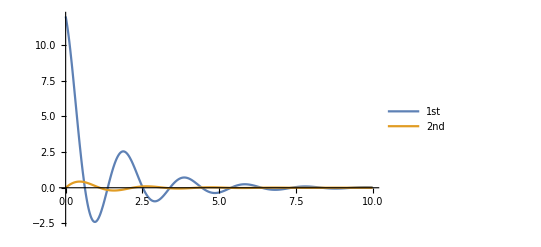

```mathematica
replacementRules={Subscript[d, 1]->0.9,Subscript[r, 1]->0.8,Subscript[d, 2]->0.85,Subscript[r, 2]->0.92,κ->0,ϵ->0,η->0.4};
Plot[{(Subscript[d, 1]^(4n)*2Cos[8 (ϵ+η)n]
+Subscript[d, 2]^(4n)*2Cos[8 (κ+η)n]
+Subscript[d, 1]^(4n) Subscript[d, 2]^(4n)*2Cos[8(ϵ-κ)n]
+Subscript[d, 1]^(4n) Subscript[d, 2]^(4n)*2Cos[8(ϵ+κ)n]
+Subscript[d, 2]^(4n) Subscript[r, 1]^(4n)*2Cos[8  (η-κ)n]
+Subscript[d, 1]^(4n) Subscript[r, 2]^(4n)*2Cos[8  (ϵ-η)n])/.replacementRules,(2*Re[((-1+Subscript[r, 1]) ((ⅇ^(8 ⅈ (η+κ)) Subscript[d, 2]^4)^n-(ⅇ^(-8 ⅈ (η-κ)) Subscript[d, 2]^4 Subscript[r, 1]^4)^n))/(ⅇ^(4 ⅈ η)+Subscript[r, 1])]
+2*Re[((-1+Subscript[r, 2]) ((ⅇ^(8 ⅈ (η+ϵ)) Subscript[d, 1]^4)^n-(ⅇ^(-8 ⅈ (η-ϵ)) Subscript[d, 1]^4 Subscript[r, 2]^4)^n))/(ⅇ^(4 ⅈ η)+Subscript[r, 2])])/.replacementRules},{n,0,10},PlotRange->All,PlotLegends->{"1st", "2nd"}]
```

Fidelity with ++ state:

```mathematica
state=Flatten[{1,1}⊗{1,1}/2];
plusPlusFidelity=Refine[state.(ρn/.Subscript[b, i_,j_]:>1/4).state,n∈Integers]//Simplify
```

1/16 (1+(ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^n+(ⅇ^(8 ⅈ (ϵ+η)) d_1^4)^n+(ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n+(ⅇ^(8 ⅈ (η+κ)) d_2^4)^n+(ⅇ^(-8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ-κ)) d_1^4 d_2^4)^n+(ⅇ^(-8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n+(ⅇ^(8 ⅈ (ϵ+κ)) d_1^4 d_2^4)^n+(-1+r_1)^(4 n)+(ⅇ^(-8 ⅈ (η-κ)) d_2^4 (-1+r_1)^4)^n+(ⅇ^(8 ⅈ (η-κ)) d_2^4 (-1+r_1)^4)^n+(ⅇ^(4 ⅈ η) ((ⅇ^(-8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(8 ⅈ (η-κ)) d_2^4 (-1+r_1)^4)^n) r_1)/(-1-ⅇ^(4 ⅈ η)+ⅇ^(4 ⅈ η) r_1)+(-1+r_2)^(4 n)+(ⅇ^(-8 ⅈ (ϵ-η)) d_1^4 (-1+r_2)^4)^n+(ⅇ^(8 ⅈ (ϵ-η)) d_1^4 (-1+r_2)^4)^n+((-1+r_1)^4 (-1+r_2)^4)^n-(((ⅇ^(8 ⅈ (η+κ)) d_2^4)^n-(ⅇ^(-8 ⅈ (η-κ)) d_2^4 (-1+r_1)^4)^n) r_1 UnitStep[-1+n])/(1+ⅇ^(4 ⅈ η)-r_1)-(-1+r_1)^(4 n) (-1+(-1+r_2)^(4 n)) UnitStep[-1+n]+((-1+r_2)^(4 n)-((-1+r_1)^4 (-1+r_2)^4)^n) UnitStep[-1+n]-(-3+2 (-1+r_1)^(4 n)+2 (-1+r_2)^(4 n)-((-1+r_1)^4 (-1+r_2)^4)^n) UnitStep[-1+n]+(ⅇ^(-4 ⅈ (2 ϵ+η)) r_2 (d_1^4 (ⅇ^(-8 ⅈ (ϵ+η)) d_1^4)^(-1+n) UnitStep[-2+n]-ⅇ^(8 ⅈ (ϵ+η)) (ⅇ^(-8 ⅈ (ϵ-η)) d_1^4 (-1+r_2)^4)^n UnitStep[-2+n]+d_1^4 UnitStep[1-n] UnitStep[-1+n]))/(-1-ⅇ^(4 ⅈ η)+ⅇ^(4 ⅈ η) r_2)+(ⅇ^(-8 ⅈ η) r_2 (-ⅇ^(8 ⅈ (η+n (ϵ+η))) d_1^(4 n) UnitStep[-2+n]+ⅇ^(8 ⅈ η) (ⅇ^(8 ⅈ (ϵ-η)) d_1^4 (-1+r_2)^4)^n UnitStep[-2+n]+ⅇ^(8 ⅈ ϵ) d_1^4 (-1+r_2)^4 UnitStep[1-n] UnitStep[-1+n]))/(1+ⅇ^(4 ⅈ η)-r_2))

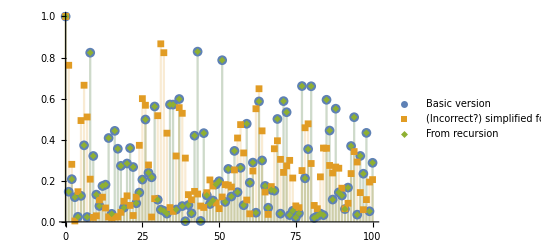

```mathematica
$Assumptions={{ϵ,η,κ,α,β,γ}∈Reals};
numericalRules={ϵ->0.1,η->0.01,κ->0.5};
DiscretePlot[{
Abs[(Exp[ⅈ 4k(-ϵ+η+κ)]+Exp[ⅈ 4k(ϵ-η+κ)]+Exp [ⅈ 4k(ϵ+η-κ)]+Exp[-ⅈ 4k(ϵ+η+κ)])/4]^2/.numericalRules,
Abs[Cos[k ϵ]Cos[k η]Cos[k κ]+ⅈ Sin[k ϵ]Sin[k η]Sin[k κ]]^2/.numericalRules,
plusPlusFidelity/.angleSubstitions/.simplifyingRules/.numericalRules/.n->k
(*Abs[1/16 (4+(ⅇ^(-8 ⅈ (ϵ-η)))^n+(ⅇ^(8 ⅈ (ϵ-η)))^n+(ⅇ^(-8 ⅈ (ϵ+η)))^n+(ⅇ^(8 ⅈ (ϵ+η)))^n+(ⅇ^(-8 ⅈ (ϵ-κ)))^n+(ⅇ^(8 ⅈ (ϵ-κ)))^n+(ⅇ^(-8 ⅈ (η-κ)))^n+(ⅇ^(8 ⅈ (η-κ)))^n+(ⅇ^(-8 ⅈ (ϵ+κ)))^n+(ⅇ^(8 ⅈ (ϵ+κ)))^n+(ⅇ^(-8 ⅈ (η+κ)))^n+(ⅇ^(8 ⅈ (η+κ)))^n)]/.n->k/.numericalRules*)
},{k,0,100},PlotLegends->{"Basic version","(Incorrect?) simplified formula", "From recursion"},PlotMarkers->{{Automatic,Medium},{Automatic,Small},{Automatic,Small}}]
```

```mathematica
(-(ⅇ^(-8 ⅈ η) (-1+Subscript[r, 2]) (ⅇ^(8 ⅈ ϵ) Subscript[d, 1]^4 Subscript[r, 2]^4 UnitStep[1-n]-ⅇ^(8 ⅈ (η+n (ϵ+η))) Subscript[d, 1]^(4 n) UnitStep[-2+n]+ⅇ^(8 ⅈ η) (ⅇ^(8 ⅈ (ϵ-η)) Subscript[d, 1]^4 Subscript[r, 2]^4)^n UnitStep[-2+n]))/(ⅇ^(4 ⅈ η)+Subscript[r, 2])+(ⅇ^(-4 ⅈ (2 ϵ+η)) (-1+Subscript[r, 2]) (Subscript[d, 1]^4 UnitStep[1-n]+ⅇ^(8 ⅈ (ϵ+η)) ((ⅇ^(-8 ⅈ (ϵ+η)) Subscript[d, 1]^4)^n-(ⅇ^(-8 ⅈ (ϵ-η)) Subscript[d, 1]^4 Subscript[r, 2]^4)^n) UnitStep[-2+n]))/(1+ⅇ^(4 ⅈ η) Subscript[r, 2]))-(2*Re[((-1+Subscript[r, 2]) ((ⅇ^(8 ⅈ (η+ϵ)) Subscript[d, 1]^4)^n-(ⅇ^(-8 ⅈ (η-ϵ)) Subscript[d, 1]^4 Subscript[r, 2]^4)^n))/(ⅇ^(4 ⅈ η)+Subscript[r, 2])])/.{Subscript[r, 2]->RandomReal[{0,1},1],Subscript[d, 1]->RandomReal[{0,1},1],n->RandomInteger[100],ϵ->RandomReal[{0,π},1],η->RandomReal[{0,π},1]}//N
```

{3.31776×10^-85+4.58454×10^-85 ⅈ}